## Section 1

#### Basic Functions

```mathematica
(* format -> style -> section *)
```

```mathematica
2+3
```

5

```mathematica
2+3
```

5

```mathematica
(* instead of number pad enter, we can press shift+alphabet pad enter to evaluate *)
```

```mathematica
2 3 
Multiplication: space
```

6

```mathematica
2/3
```

```mathematica
Division: Ctrl + /
```

2/3

```mathematica
2/3
```

2/3

```mathematica
√144
```

```mathematica
Squareroot: Ctrl+2
```

12

```mathematica
π // N
```

3.14159

```mathematica
(* Delete cell: shift+del *)
```

```mathematica
Sin[π/12]
```

```mathematica
(* Use capital first letter for the function name and square brackets for its argument *)
```

(-1+√3)/(2 √2)

```mathematica
a=1
(* Variable *)
```

```mathematica
∞
(* esc+\ for Hbar, Infinity, Gamma, Delta, Theta *)
```

∞

#### MATRIX

```mathematica
List
(* Think of it as a vector*)
```

```mathematica
a= List[1,2,3,4]
```

{1,2,3,4}

```mathematica
b= {1,2,3,4}
```

{1,2,3,4}

```mathematica
a+b
```

{2,4,6,8}

```mathematica
a==b
```

True

```mathematica
Power [144,1/2]
```

12

```mathematica
FullForm[√155]
(* FullForm to know how Mathematica performs it *)
```

Power[155,Rational[1,2]]

```mathematica
FullForm[{1,2,3,4}]
```

List[1,2,3,4]

```mathematica
{{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
SetOptions[$FrontEnd, CommonDefaultFormatTypes -> {"Output" -> TraditionalForm}]
```

```mathematica
(* Now the output will be shown in traditional form; automatically the output will be in MatrixForm*)
```

```mathematica
m= {{1,2},{3,4}}
```

```mathematica
({{1, 2}, {3, 4}})
```

(1 | 2
3 | 4)

```mathematica
Det[m]
```

-2

```mathematica
Inverse[m]
```

(-2 | 1
3/2 | -1/2)

```mathematica
m.{1,2}
```

```mathematica
(* Matrix multiplication "." *)
```

{5,11}

```mathematica
m.m.m.m
```

(199 | 290
435 | 634)

```mathematica
MatrixExp[m]
```

(1/2 ⅇ^(5/2-(√33)/2)+1/2 √(3/11) ⅇ^(5/2-(√33)/2)+1/2 ⅇ^(5/2+(√33)/2)-1/2 √(3/11) ⅇ^(5/2+(√33)/2) | -(2 ⅇ^(5/2-(√33)/2))/(√33)+(2 ⅇ^(5/2+(√33)/2))/(√33)
-√(3/11) ⅇ^(5/2-(√33)/2)+√(3/11) ⅇ^(5/2+(√33)/2) | 1/2 ⅇ^(5/2-(√33)/2)-1/2 √(3/11) ⅇ^(5/2-(√33)/2)+1/2 ⅇ^(5/2+(√33)/2)+1/2 √(3/11) ⅇ^(5/2+(√33)/2))

```mathematica
MatrixExp[m]//N
```

(51.969 | 74.7366
112.105 | 164.074)

```mathematica
f[4]
```

f(4)

```mathematica
f@4
```

f(4)

```mathematica
4//f
```

f(4)

```mathematica
(* N@expression= N[expression] = expression//N *)
```

```mathematica
Table[i,{i, 1,100}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Table[Sin(i^2),{i, 1,100}]
```

{Sin,4 Sin,9 Sin,16 Sin,25 Sin,36 Sin,49 Sin,64 Sin,81 Sin,100 Sin,121 Sin,144 Sin,169 Sin,196 Sin,225 Sin,256 Sin,289 Sin,324 Sin,361 Sin,400 Sin,441 Sin,484 Sin,529 Sin,576 Sin,625 Sin,676 Sin,729 Sin,784 Sin,841 Sin,900 Sin,961 Sin,1024 Sin,1089 Sin,1156 Sin,1225 Sin,1296 Sin,1369 Sin,1444 Sin,1521 Sin,1600 Sin,1681 Sin,1764 Sin,1849 Sin,1936 Sin,2025 Sin,2116 Sin,2209 Sin,2304 Sin,2401 Sin,2500 Sin,2601 Sin,2704 Sin,2809 Sin,2916 Sin,3025 Sin,3136 Sin,3249 Sin,3364 Sin,3481 Sin,3600 Sin,3721 Sin,3844 Sin,3969 Sin,4096 Sin,4225 Sin,4356 Sin,4489 Sin,4624 Sin,4761 Sin,4900 Sin,5041 Sin,5184 Sin,5329 Sin,5476 Sin,5625 Sin,5776 Sin,5929 Sin,6084 Sin,6241 Sin,6400 Sin,6561 Sin,6724 Sin,6889 Sin,7056 Sin,7225 Sin,7396 Sin,7569 Sin,7744 Sin,7921 Sin,8100 Sin,8281 Sin,8464 Sin,8649 Sin,8836 Sin,9025 Sin,9216 Sin,9409 Sin,9604 Sin,9801 Sin,10000 Sin}

```mathematica
Table[Sin(i^2+j^2)//N,{i, 1,10},{j,2,10}]
```

(5. Sin | 10. Sin | 17. Sin | 26. Sin | 37. Sin | 50. Sin | 65. Sin | 82. Sin | 101. Sin
8. Sin | 13. Sin | 20. Sin | 29. Sin | 40. Sin | 53. Sin | 68. Sin | 85. Sin | 104. Sin
13. Sin | 18. Sin | 25. Sin | 34. Sin | 45. Sin | 58. Sin | 73. Sin | 90. Sin | 109. Sin
20. Sin | 25. Sin | 32. Sin | 41. Sin | 52. Sin | 65. Sin | 80. Sin | 97. Sin | 116. Sin
29. Sin | 34. Sin | 41. Sin | 50. Sin | 61. Sin | 74. Sin | 89. Sin | 106. Sin | 125. Sin
40. Sin | 45. Sin | 52. Sin | 61. Sin | 72. Sin | 85. Sin | 100. Sin | 117. Sin | 136. Sin
53. Sin | 58. Sin | 65. Sin | 74. Sin | 85. Sin | 98. Sin | 113. Sin | 130. Sin | 149. Sin
68. Sin | 73. Sin | 80. Sin | 89. Sin | 100. Sin | 113. Sin | 128. Sin | 145. Sin | 164. Sin
85. Sin | 90. Sin | 97. Sin | 106. Sin | 117. Sin | 130. Sin | 145. Sin | 162. Sin | 181. Sin
104. Sin | 109. Sin | 116. Sin | 125. Sin | 136. Sin | 149. Sin | 164. Sin | 181. Sin | 200. Sin)

```mathematica
(*Table[Function,{row,start number, end number},{column,start number,end number}]*)
```

#### PLOT

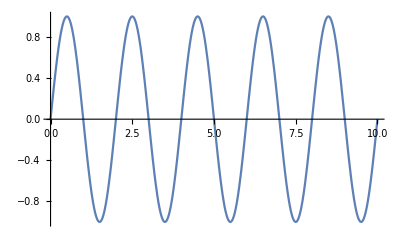

```mathematica
Plot[Sin[x*π],{x,0,10}]
```

#### To know more about a function

```mathematica
?Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

```mathematica
?Table
```

Table[expr,{i_max}] generates a list of i_max copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
?*Plot*
```

```mathematica
(* ? before any function to know its what it does and how its used*)
```

```mathematica
(* ?*expression means the expression is at the end of the function
?expression* means the expression is at the start of the function
?*expression* means the expression is at the end of the function *)
```